```mathematica
Clear[s,x,Phi,a,b,c,d]
```

```mathematica
s0[1]={{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
s0[2]={{I,0},{0,-I}}
```

{{ⅈ,0},{0,-ⅈ}}

```mathematica
s0[3]={{0,-1},{1,0}}
```

{{0,-1},{1,0}}

```mathematica
s0[4]={{0,I},{I,0}}
```

{{0,ⅈ},{ⅈ,0}}

```mathematica
Table[Det[s[i]],{i,4}]
```

{Det[s[1]],Det[s[2]],Det[s[3]],Det[s[4]]}

```mathematica
Table[Tr[s[i]],{i,4}]
```

{Tr[s[1]],Tr[s[2]],Tr[s[3]],Tr[s[4]]}

```mathematica
Sum[s[i].s[i],{i,4}]
```

s[1].s[1]+s[2].s[2]+s[3].s[3]+s[4].s[4]

```mathematica
(* 17 element (U(1)*SU(2))^4 Chiral group*)
```

```mathematica
s[1]=IdentityMatrix[4]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
s[2]={{I,0,0,0},
{0,-I,0,0},
{0,0,I,0},
{0,0,0,-I}}
```

{{ⅈ,0,0,0},{0,-ⅈ,0,0},{0,0,ⅈ,0},{0,0,0,-ⅈ}}

```mathematica
s[3]={{0,-1,0,0},
{1,0,0,0},
{0,0,0,-1},
{0,0,1,0}}
```

{{0,-1,0,0},{1,0,0,0},{0,0,0,-1},{0,0,1,0}}

```mathematica
s[4]={{0,I,0,0},
{I,0,0,0},
{0,0,0,I},
{0,0,I,0}}
```

{{0,ⅈ,0,0},{ⅈ,0,0,0},{0,0,0,ⅈ},{0,0,ⅈ,0}}

```mathematica
s[5]={{I,0,0,0},
{0,-I,0,0},
{0,0,I,0},
{0,0,0,-I}}
```

{{ⅈ,0,0,0},{0,-ⅈ,0,0},{0,0,ⅈ,0},{0,0,0,-ⅈ}}

```mathematica
s[6]={{-1,0,0,0},
{0,-1,0,0},
{0,0,-1,0},
{0,0,0,-1}}
```

{{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}

```mathematica
s0[2].s0[3]
```

{{0,-ⅈ},{-ⅈ,0}}

```mathematica
s[7]={{0,-I,0,0},
{-I,0,0,0},
{0,0,0,-I},
{0,0,-I,0}}
```

{{0,-ⅈ,0,0},{-ⅈ,0,0,0},{0,0,0,-ⅈ},{0,0,-ⅈ,0}}

```mathematica
s0[2].s0[4]
```

{{0,-1},{1,0}}

```mathematica
s[8]={{0,-1,0,0},
{1,0,0,0},
{0,0,0,-1},
{0,0,1,0}}
```

{{0,-1,0,0},{1,0,0,0},{0,0,0,-1},{0,0,1,0}}

```mathematica
s0[3].s0[1]
```

{{0,-1},{1,0}}

```mathematica
s[9]={{0,-1,0,0},
{1,0,0,0},
{0,0,0,-1},
{0,0,1,0}}
```

{{0,-1,0,0},{1,0,0,0},{0,0,0,-1},{0,0,1,0}}

```mathematica
s0[3].s0[2]
```

{{0,ⅈ},{ⅈ,0}}

```mathematica
s[10]={{0,-1,0,0},
{1,0,0,0},
{0,0,0,-1},
{0,0,1,0}}
```

{{0,-1,0,0},{1,0,0,0},{0,0,0,-1},{0,0,1,0}}

```mathematica
s0[3].s0[3]
```

{{-1,0},{0,-1}}

```mathematica
s[11]={{-1,0,0,0},
{0,-1,0,0},
{0,0,-1,0},
{0,0,0,-1}}
```

{{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}

```mathematica
s0[3].s0[4]
```

{{-ⅈ,0},{0,ⅈ}}

```mathematica
s[12]=-{{I,0,0,0},
{0,-I,0,0},
{0,0,I,0},
{0,0,0,-I}}
```

{{-ⅈ,0,0,0},{0,ⅈ,0,0},{0,0,-ⅈ,0},{0,0,0,ⅈ}}

```mathematica
s0[4].s0[1]
```

{{0,ⅈ},{ⅈ,0}}

```mathematica
s[13]={{0,I,0,0},
{I,0,0,0},
{0,0,0,I},
{0,0,I,0}}
```

{{0,ⅈ,0,0},{ⅈ,0,0,0},{0,0,0,ⅈ},{0,0,ⅈ,0}}

```mathematica
s0[4].s0[2]
```

{{0,1},{-1,0}}

```mathematica
s[14]={{0,-1,0,0},
{1,0,0,0},
{0,0,0,-1},
{0,0,1,0}}
```

{{0,-1,0,0},{1,0,0,0},{0,0,0,-1},{0,0,1,0}}

```mathematica
s0[4].s0[3]
```

{{ⅈ,0},{0,-ⅈ}}

```mathematica
s[15]={{I,0,0,0},
{0,-I,0,0},
{0,0,I,0},
{0,0,0,-I}}
```

{{ⅈ,0,0,0},{0,-ⅈ,0,0},{0,0,ⅈ,0},{0,0,0,-ⅈ}}

```mathematica
s0[4].s0[4]
```

{{-1,0},{0,-1}}

```mathematica
s[16]={{-1,0,0,0},
{0,-1,0,0},
{0,0,-1,0},
{0,0,0,-1}}
```

{{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}

```mathematica
s[17]=Apply[Dot,Table[s[i],{i,16}]]
```

{{ⅈ,0,0,0},{0,-ⅈ,0,0},{0,0,ⅈ,0},{0,0,0,-ⅈ}}

```mathematica
Table[Det[s[i]],{i,17}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Table[Tr[s[i]],{i,17}]
```

{4,0,0,0,0,-4,0,0,0,0,-4,0,0,0,0,-4,0}

```mathematica
(*Casimir Invariant*)
```

```mathematica
Sum[s[i].s[i],{i,17}]
```

{{-9,0,0,0},{0,-9,0,0},{0,0,-9,0},{0,0,0,-9}}

```mathematica
(*Killing vectors*)
```

```mathematica
ki=Table[s[i].{1,1,1,-1},{i,17}]
```

{{1,1,1,-1},{ⅈ,-ⅈ,ⅈ,ⅈ},{-1,1,1,1},{ⅈ,ⅈ,-ⅈ,ⅈ},{ⅈ,-ⅈ,ⅈ,ⅈ},{-1,-1,-1,1},{-ⅈ,-ⅈ,ⅈ,-ⅈ},{-1,1,1,1},{-1,1,1,1},{-1,1,1,1},{-1,-1,-1,1},{-ⅈ,ⅈ,-ⅈ,-ⅈ},{ⅈ,ⅈ,-ⅈ,ⅈ},{-1,1,1,1},{ⅈ,-ⅈ,ⅈ,ⅈ},{-1,-1,-1,1},{ⅈ,-ⅈ,ⅈ,ⅈ}}

```mathematica
kit=Transpose[ki]
```

{{1,ⅈ,-1,ⅈ,ⅈ,-1,-ⅈ,-1,-1,-1,-1,-ⅈ,ⅈ,-1,ⅈ,-1,ⅈ},{1,-ⅈ,1,ⅈ,-ⅈ,-1,-ⅈ,1,1,1,-1,ⅈ,ⅈ,1,-ⅈ,-1,-ⅈ},{1,ⅈ,1,-ⅈ,ⅈ,-1,ⅈ,1,1,1,-1,-ⅈ,-ⅈ,1,ⅈ,-1,ⅈ},{-1,ⅈ,1,ⅈ,ⅈ,1,-ⅈ,1,1,1,1,-ⅈ,ⅈ,1,ⅈ,1,ⅈ}}

```mathematica
ca=Table[2*ki[[i]].ki[[j]]/(ki[[i]].ki[[i]]),{i,17},{j,17}]
```

{{2,0,0,0,0,-2,0,0,0,0,-2,0,0,0,0,-2,0},{0,2,0,0,2,0,0,0,0,0,0,-2,0,0,2,0,2},{0,0,2,0,0,0,0,2,2,2,0,0,0,2,0,0,0},{0,0,0,2,0,0,-2,0,0,0,0,0,2,0,0,0,0},{0,2,0,0,2,0,0,0,0,0,0,-2,0,0,2,0,2},{-2,0,0,0,0,2,0,0,0,0,2,0,0,0,0,2,0},{0,0,0,-2,0,0,2,0,0,0,0,0,-2,0,0,0,0},{0,0,2,0,0,0,0,2,2,2,0,0,0,2,0,0,0},{0,0,2,0,0,0,0,2,2,2,0,0,0,2,0,0,0},{0,0,2,0,0,0,0,2,2,2,0,0,0,2,0,0,0},{-2,0,0,0,0,2,0,0,0,0,2,0,0,0,0,2,0},{0,-2,0,0,-2,0,0,0,0,0,0,2,0,0,-2,0,-2},{0,0,0,2,0,0,-2,0,0,0,0,0,2,0,0,0,0},{0,0,2,0,0,0,0,2,2,2,0,0,0,2,0,0,0},{0,2,0,0,2,0,0,0,0,0,0,-2,0,0,2,0,2},{-2,0,0,0,0,2,0,0,0,0,2,0,0,0,0,2,0},{0,2,0,0,2,0,0,0,0,0,0,-2,0,0,2,0,2}}

```mathematica
Det[ca]//Chop
```

0

```mathematica
Tr[ca]
```

34

```mathematica
Eigenvalues[ca]
```

{10,10,8,6,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
p[x_]=Expand[CharacteristicPolynomial[ca,x]/x^13]
```

-4800+2360 x-428 x^2+34 x^3-x^4

```mathematica
NSolve[D[p[x],{x,1}]==0,x]
```

{{x→6.71922},{x→8.78078},{x→10.}}

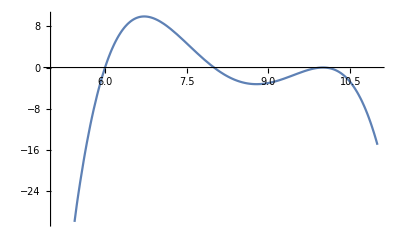

```mathematica
Plot[p[x],{x,5,11}]
```

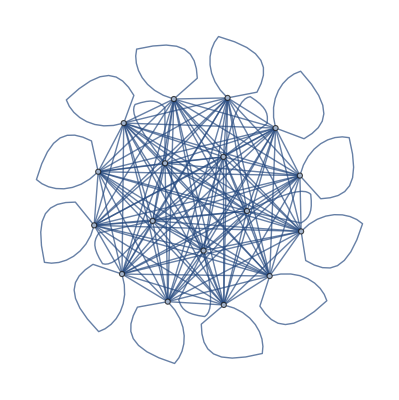

```mathematica
WeightedAdjacencyGraph[ca]
```

```mathematica
AdjacencyGraph[Abs[ca]]
```

-Graphics-

```mathematica
(*end*)
```